```mathematica
h=1/10;
m=2;
V[x_]:=x^2 - 0.5*x^4

V1[x_]:=4*(Exp[-2*x]-2*Exp[-x])
ℒ=-(h^2/(2*m))*u''[x]+V[x]*u[x];
```

```mathematica
{vals,funs}=NDEigensystem[ℒ,u[x],{x,0,3},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.0490167,0.13013,-0.161806,0.236259,0.369657,0.401103,-0.497333,0.513146,0.566027,0.662089,0.766403,-0.872692,0.883809,1.01227,1.15098,-1.28596,1.29939,1.45704,1.62357,-1.73618,1.79869,1.98213,2.17369,-2.223,2.37315,2.58036,-2.74653,2.79516,3.01742,3.24701,-3.30722,3.48382,3.72775,-3.90586,3.97871,4.2366,4.50136,-4.54352,4.77291,5.05119,-5.22158,5.33612,5.62766,5.92575,-5.94175,6.23034,6.54139,-6.70611,6.85884,7.18267}

```mathematica
Sort[vals]
```

{-6.70611,-5.94175,-5.22158,-4.54352,-3.90586,-3.30722,-2.74653,-2.223,-1.73618,-1.28596,-0.872692,-0.497333,-0.161806,0.0490167,0.13013,0.236259,0.369657,0.401103,0.513146,0.566027,0.662089,0.766403,0.883809,1.01227,1.15098,1.29939,1.45704,1.62357,1.79869,1.98213,2.17369,2.37315,2.58036,2.79516,3.01742,3.24701,3.48382,3.72775,3.97871,4.2366,4.50136,4.77291,5.05119,5.33612,5.62766,5.92575,6.23034,6.54139,6.85884,7.18267}

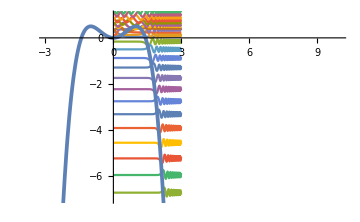

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,0,4}],Plot[V[x],{x,-3,10}, PlotStyle->{Thickness[0.0075]}],PlotRange->{-7,1},AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
eps_morse=Table[-(2-n-1/2)^2,{n,0,10}]//N
```

{-2.25,-0.25,-0.25,-2.25,-6.25,-12.25,-20.25,-30.25,-42.25,-56.25,-72.25}

```mathematica
eps_qho=Table[h*2*(n+1/2),{n,0,10}]//N
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1}

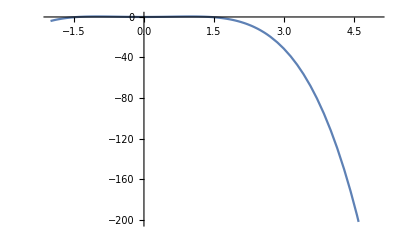

```mathematica
Plot[V[x],{x,-2,5}]
```

```mathematica
lambda={0.05,0.06,0.07,0.08,0.09,0.1,0.12,0.15,0.2,0.25,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}
```

{0.05,0.06,0.07,0.08,0.09,0.1,0.12,0.15,0.2,0.25,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}

```mathematica
E0={0.0000146,0.000119,0.000521,0.00154,0.00349,0.0066,0.0165,0.039,0.09,0.14,0.19,0.27,0.35,0.42,0.48,0.53,0.58,0.62}
```

{0.0000146,0.000119,0.000521,0.00154,0.00349,0.0066,0.0165,0.039,0.09,0.14,0.19,0.27,0.35,0.42,0.48,0.53,0.58,0.62}

```mathematica
data=Transpose@{-lambda,E0};
datashort=Transpose@{-lambda[[1;;5]],E0[[1;;5]]}
```

{{-0.05,0.0000146},{-0.06,0.000119},{-0.07,0.000521},{-0.08,0.00154},{-0.09,0.00349}}

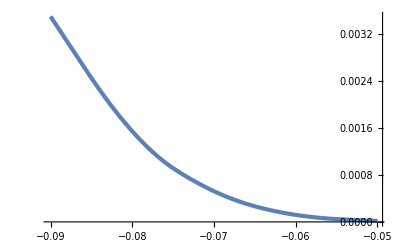

```mathematica
ListPlot[datashort, Joined->True, InterpolationOrder->2, PlotStyle->{Thickness[0.0075]}]
```

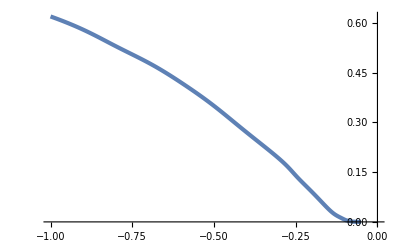

```mathematica
ListPlot[data, Joined->True, InterpolationOrder->6, PlotStyle->{Thickness[0.0075]}]
```

```mathematica
model=LinearModelFit[datashort,x,x]
```

FittedModel[-0.00472334-0.083718 x]

```mathematica
BW[eps_]:=(2/Sqrt[2*π])*Exp[-1/(3*eps)]*(1/Sqrt[eps])
```

```mathematica
BW[0.05/4]
```

1.87197×10^-11

```mathematica
epsDrum[epsBW_]:=4*epsBW
```

```mathematica
BWexact=Table[ ω*Sqrt[6/π]*Sqrt[(4*ω^3)/(3*-4*lambda[[i]]  )]  *Exp[-4*ω^3 /(3*4*lambda[[i]] )], {i,1,18} ]
```

{0.+5.49044×10^-8 ⅈ,0.+1.16111×10^-6 ⅈ,0.+0.000010146 ⅈ,0.+0.0000511061 ⅈ,0.+0.000178479 ⅈ,0.+0.000482681 ⅈ,0.+0.00212079 ⅈ,0.+0.00912999 ⅈ,0.+0.0380565 ⅈ,0.+0.0873837 ⅈ,0.+0.149558 ⅈ,0.+0.284155 ⅈ,0.+0.40722 ⅈ,0.+0.509007 ⅈ,0.+0.589848 ⅈ,0.+0.652922 ⅈ,0.+0.701705 ⅈ,(2 ⅈ 2^(3/4) ⅇ^(-(2 √2)/3))/(√π)}

```mathematica
E0
```

{0.0000146,0.000119,0.000521,0.00154,0.00349,0.0066,0.0165,0.039,0.09,0.14,0.19,0.27,0.35,0.42,0.48,0.53,0.58,0.62}

```mathematica
BWexact[[1]]/E0[[1]]
```

0.+0.00376058 ⅈ

```mathematica
km[h_,c_]:=((2*h^2*Sqrt[h^6/(2*c^2)])/(Sqrt[2*π]))*Exp[-h^6/(6*c^2)]
```

```mathematica
kmcoeff=Table[km[Sqrt[2], Sqrt[2*lambda[[i]]]  ], {i,1,18}]
```

{0.0000163458,0.000137694,0.000623445,0.00191787,0.00456423,0.00908215,0.0251853,0.0684292,0.18002,0.313615,0.446504,0.673955,0.84128,0.959091,1.04069,1.09655,1.13413,4/(ⅇ^(2/3) √π)}

```mathematica
E0
```

{0.0000146,0.000119,0.000521,0.00154,0.00349,0.0066,0.0165,0.039,0.09,0.14,0.19,0.27,0.35,0.42,0.48,0.53,0.58,0.62}

{0.0000146,0.000119,0.000521,0.00154,0.00349,0.0066,0.0165,0.039,0.09,0.14,0.19,0.27,0.35,0.42,0.48,0.53,0.58,0.62}

```mathematica
BW[lambda[[1]]]
```

0.00454107

```mathematica
km[1, Sqrt[lambda[[1]]/2]]//N
```

0.00454107

```mathematica
datadrum=Transpose@{lambda,E0};
databw= Transpose@{lambda,kmcoeff};
```

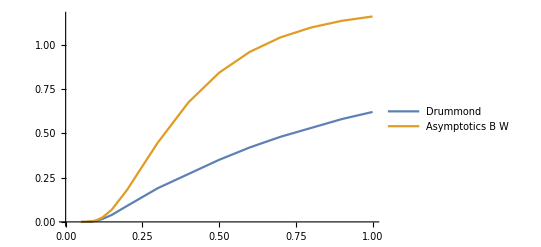

```mathematica
ListLinePlot[{datadrum,databw}, PlotLegends->{Drummond, B W  Asymptotics}]
```

```mathematica
datadrumshort=Transpose@{lambda[[1;;5]],E0[[1;;5]]};
databwshort= Transpose@{lambda[[1;;5]],kmcoeff[[1;;5]]};
```

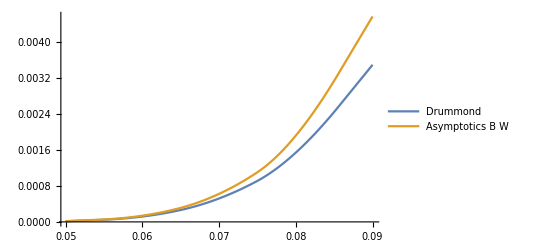

```mathematica
ListLinePlot[{datadrumshort,databwshort}, PlotLegends->{Drummond, B W  Asymptotics}, InterpolationOrder->2]
```

```mathematica
BW[0.05]//N
```

0.00454107

```mathematica
km[Sqrt[2], 4*0.05]//N
```

5.32706×10^-14

```mathematica
BW[1]//N
```

0.571709

```mathematica
E0[[1]]
```

0.0000146

```mathematica
lambda[[1]]
```

0.05